```mathematica
nMax=1000;
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
fib[77,7,24,8282]
```

Part::partd: Part specification 1 ⟦ 1 ⟧ is longer than depth of object.

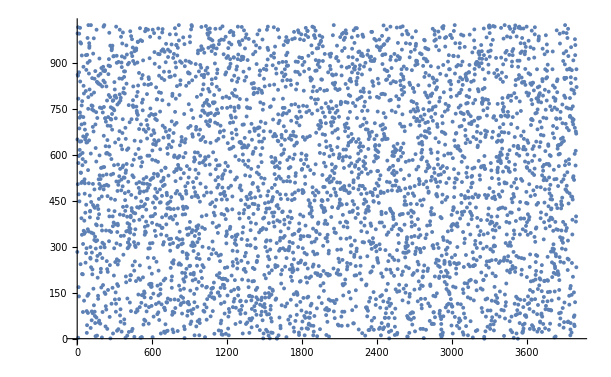
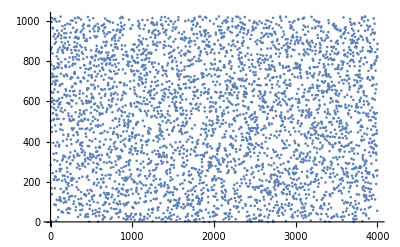
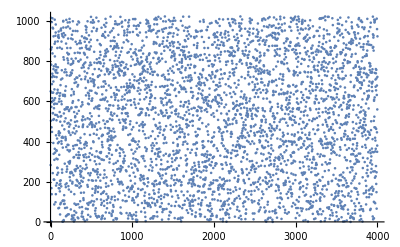
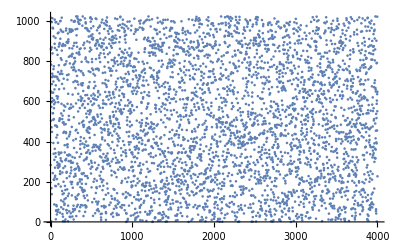
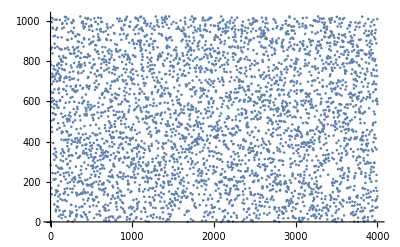
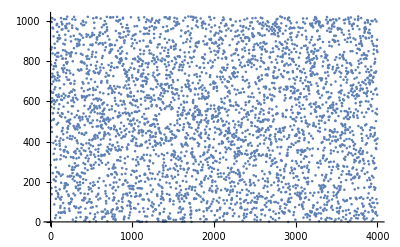
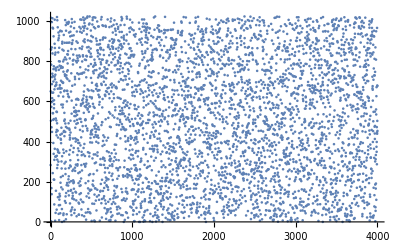
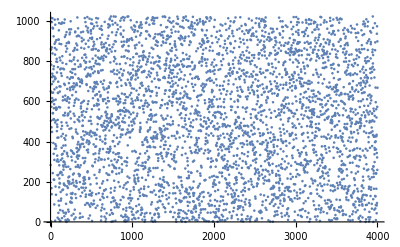
{{{-Graphics-,p=23,q=50},{-Graphics-,p=23,q=51},{-Graphics-,p=23,q=52},{-Graphics-,p=23,q=53},{-Graphics-,p=23,q=54},{-Graphics-,p=23,q=55},{-Graphics-,p=23,q=56},{-Graphics-,p=23,q=57}},{{-Graphics-,p=24,q=50},{-Graphics-,p=24,q=51},{-Graphics-,p=24,q=52},{-Graphics-,p=24,q=53},{-Graphics-,p=24,q=54},{-Graphics-,p=24,q=55},{-Graphics-,p=24,q=56},{-Graphics-,p=24,q=57}},{{-Graphics-,p=25,q=50},{-Graphics-,p=25,q=51},{-Graphics-,p=25,q=52},{-Graphics-,p=25,q=53},{-Graphics-,p=25,q=54},{-Graphics-,p=25,q=55},{-Graphics-,p=25,q=56},{-Graphics-,p=25,q=57}},{{-Graphics-,p=26,q=50},{-Graphics-,p=26,q=51},{-Graphics-,p=26,q=52},{-Graphics-,p=26,q=53},{-Graphics-,p=26,q=54},{-Graphics-,p=26,q=55},{-Graphics-,p=26,q=56},{-Graphics-,p=26,q=57}},{{-Graphics-,p=27,q=50},{-Graphics-,p=27,q=51},{-Graphics-,p=27,q=52},{-Graphics-,p=27,q=53},{-Graphics-,p=27,q=54},{-Graphics-,p=27,q=55},{-Graphics-,p=27,q=56},{-Graphics-,p=27,q=57}},{{-Graphics-,p=28,q=50},{-Graphics-,p=28,q=51},{-Graphics-,p=28,q=52},{-Graphics-,p=28,q=53},{-Graphics-,p=28,q=54},{-Graphics-,p=28,q=55},{-Graphics-,p=28,q=56},{-Graphics-,p=28,q=57}},{{-Graphics-,p=29,q=50},{-Graphics-,p=29,q=51},{-Graphics-,p=29,q=52},{-Graphics-,p=29,q=53},{-Graphics-,p=29,q=54},{-Graphics-,p=29,q=55},{-Graphics-,p=29,q=56},{-Graphics-,p=29,q=57}}}

```mathematica
nMax=4000;
modulo = 2^10;
seq = Table[RandomInteger[modulo],{i,1,57}];
fib[x_,p_,q_,m_]:=RecurrenceTable[{X[n]==Mod[X[n-p]+X[n-q],m],Table[X[i]==x[[i]],{i,1,q}]},X,{n,1,nMax}];
Table[{ListPlot[fib[seq,p,q,modulo]],"p="~~ToString[p],"q="~~ToString[q]},{p,23,29},{q,50,57}]
```